# Test computation method for EWPT

Isaac R Wang

This code tests different computation methods for the EWPT strength.
Since the model is SM with small Higgs at high energy scale, an arbitrarily light Higgs and a lighter smaller top Yukawa coupling is applied here. Slightly smaller gauge couplings are also applied.
Main refs: hep-ph/9203203, hep-ph/9212235, 2205.08815

## The 1-loop perturbation theory in 3d

Ref: the DRalgo package (arXiv:2205.08815)

### Preparison

```mathematica
SetDirectory[NotebookDirectory[]];
$LoadGroupMath=True;
<<DRalgo`
```

-Graphics- | DRDRDRDRDRDRDRDRDRDRDRDRDRDR DRalgo DRDRDRDRDRDRDRDRDRDRDRDRDRDRDVersion: 1.01 beta (16-05-2022)Authors: Andreas Ekstedt, Philipp Schicho, Tuomas V.I. TenkanenReference: 2205.08815 [hep-ph]Repository link: https://github.com/DR-algo/DRalgoDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRD

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

GroupMath is an independent package, and is not part of DRalgo

Please Cite GroupMath: Comput.Phys.Commun. 267 (2021) 108085 • e-Print: 2011.01764 [hep-th]

```mathematica
Group={"SU3","SU2","U1"};
RepAdjoint={{1,1},{2},0};
HiggsDoublet={{{0,0},{1},1/2},"C"};
RepScalar={HiggsDoublet};
CouplingName={g3,g2,g1};
Rep1={{{1,0},{1},1/6},"L"}; (*qL*)
Rep2={{{1,0},{0},2/3},"R"}; (*uR*)
Rep3={{{1,0},{0},-1/3},"R"}; (*dR*)
Rep4={{{0,0},{1},-1/2},"L"}; (*lL*)
Rep5={{{0,0},{0},-1},"R"}; (*eR*)
RepFermion1Gen={Rep1,Rep2,Rep3,Rep4,Rep5};
RepFermion3Gen={RepFermion1Gen}//Flatten[#,1]&;
{gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC}=AllocateTensors[Group,RepAdjoint,CouplingName,RepFermion3Gen,RepScalar];
InputInv={{1,1},{True,False}};
MassTerm1=CreateInvariant[Group,RepScalar,InputInv][[1]];
Vmass=-μsq MassTerm1;
μij=GradMass[Vmass];
Vquartic=λ MassTerm1^2;
λ4=GradQuartic[Vquartic];
InputInv={{1,1,2},{False,False,True}};
YukawaDoublet1=CreateInvariantYukawa[Group,RepScalar,RepFermion3Gen,InputInv][[1]]//Simplify;
Ysff=-GradYukawa[yt1*YukawaDoublet1];
YsffC=Simplify[Ysff//Normal//Conjugate,Assumptions->{yt1>0}]//SparseArray;
ImportModelDRalgo[Group,gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC,Verbose->False];
(*Import model.*)
PosFermion=PrintFermionRepPositions[];
FermionMat=Table[{nF,i},{i,PosFermion}];
DefineNF[FermionMat]
PerformDRhard[](*Compute thermal masses, effective couplings, beta functions and anomalous dimensions*)
PerformDRsoft[{}](*Integrate out heavy temporal scalar*)
```

```mathematica
DefineNewTensorsUS[μij,λ4,λ3,gvss,gvvv];
ϕvev={0,0,0,ϕ}//SparseArray;
DefineVEVS[ϕvev];
MassMatrix=PrintTensorsVEV[];VectorMass=MassMatrix[[2]]//Normal;VectorEigenvectors=FullSimplify[Transpose[Normalize/@Eigenvectors[VectorMass[[11;;12,11;;12]]]],Assumptions->{g1>0,g2>0,ϕ>0}];
DVRot={{IdentityMatrix[10],0},{0,VectorEigenvectors}}//ArrayFlatten;DSRot=IdentityMatrix[4];RotateTensorsUSPostVEV[DSRot,DVRot];
CalculatePotentialUS[](*Run this to compute the potential*)
```

The Vector Mass-Matrix is not Diagonal

(1) Scalar Mass, (2) Vector Mass, (3) Scalar Quartic, (4) Scalar Cubic, (5) VSS, (6) VVS, (7) VVV

```mathematica
BetaFunctions4D[];
sub1={g1->√g1sq[Λ],g2->√g2sq[Λ],g3->√g3sq[Λ],λ->λh[Λ],μsq->μhsq[Λ],yt1->yt[Λ]};
βg1sq=g1^2/.BetaFunctions4D[]/.sub1;
βg2sq=g2^2/.BetaFunctions4D[]/.sub1;
βg3sq=g3^2/.BetaFunctions4D[]/.sub1;
βλ=λ/.BetaFunctions4D[]/.sub1//Expand;
βμsq=μsq/.BetaFunctions4D[]/.sub1//Expand;
βyt=yt1/.BetaFunctions4D[]/.sub1//Expand;
```

```mathematica
solveBetas[{g1sqInit_,g2sqInit_,g3sqInit_,ytInit_,μhsqInit_,λhInit_}]:=Block[{initialScale,Λ,nF,g1sq,g2sq,g3sq,yt,λh,μhsq,eqg1sq,eqg2sq,eqg3sq,eqyt,eqλh,eqμhsq},
nF=3;
eqg1sq=βg1sq;
eqg2sq=βg2sq;
eqg3sq=βg3sq;
eqyt=βyt;
eqλh=βλ;
eqμhsq=βμsq;
initialScale= 91.1876;
{g1sq,g2sq,g3sq,yt,μhsq,λh}=NDSolveValue[{
(*Beta functions*)
Λ D[g1sq[Λ],Λ]==eqg1sq,
Λ D[g2sq[Λ],Λ]==eqg2sq,
Λ D[g3sq[Λ],Λ]==eqg3sq,
Λ D[yt[Λ],Λ]==eqyt,
Λ D[λh[Λ],Λ]==eqλh,
Λ D[μhsq[Λ],Λ]==eqμhsq,
(*initial condition*)
g1sq[initialScale]==g1sqInit,
g2sq[initialScale]==g2sqInit,
g3sq[initialScale]==g3sqInit,
yt[initialScale]==ytInit,
λh[initialScale]==λhInit,
μhsq[initialScale]==μhsqInit
},
{g1sq,g2sq,g3sq,yt,μhsq,λh},
{Λ,5,5000}
];
Return[{g1sq,g2sq,g3sq,yt,μhsq,λh}];
]
```

```mathematica
Parameters[Temp_,scale_,g1sq_,g2sq_,g3sq_,yt_,μhsq_,λh_]:=
(*The input is the temperature, the RG-scale, and running 4d parameters.*)
Block[{nF,g1,g1sq3d,g2,g2sq3d,g3,g3sq3d,λh3d,mhsqLO,mhsqNLO,mhsq3d,Lb,Lf,numbers,gaugeDR,μhsq3d,mDsqU1,mDsqSU2,mDsqSU3,DebyemassRule,λhUS,g1sq3dUS,g2sq3dUS,g3sq3dUS,msqUSLO,msqUSNLO,μhsq3dUS},
(*Numbers. This should be applied later*)
numbers={g1->√g1sq,g2->√g2sq,g3->√g3sq,yt1->yt,μsq->μhsq,λ->λh,nF->3,μ->scale,T->Temp};

(*From 4d to 3d*)
g1sq3d=g13d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
g2sq3d=g23d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
g3sq3d=g33d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
gaugeDR={g13d->√g1sq3d,g23d->√g2sq3d,g33d->√g3sq3d};
λh3d=λ3d/.PrintCouplings[]/.PrintConstants[]/.numbers;
mhsqLO=μsq3d/.PrintScalarMass["LO"]/.PrintConstants[]/.numbers;
mhsqNLO=μsq3d/.PrintScalarMass["NLO"]/.PrintTemporalScalarCouplings[]/.{g13d->√g1sq3d,g23d->√g2sq3d,g33d->√g3sq3d,λ3d->λh3d}/.PrintConstants[]/.numbers;
μhsq3d=mhsqLO+mhsqNLO;

(*From 3d to 3d ultra soft*)
(*First get the debye masses*)
mDsqU1=(μsqU1/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqU1/.PrintDebyeMass["NLO"]/.PrintConstants[]/.numbers);
mDsqSU2=(μsqSU2/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqSU2/.PrintDebyeMass["NLO"]/.PrintConstants[]/.PrintConstants[]/.numbers);
mDsqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqSU3/.PrintDebyeMass["NLO"]/.PrintConstants[]/.numbers);
DebyemassRule={μsqSU3->mDsqSU3,μsqSU2->mDsqSU2,μsqU1->mDsqU1};

(*Then printout the couplings*)
λhUS=λ3dUS/.PrintCouplingsUS[]/.DebyemassRule/.PrintTemporalScalarCouplings[]/.gaugeDR/.PrintConstants[]/.{λ3d->λh3d}/.numbers;
g1sq3dUS=g13dUS^2/.PrintCouplingsUS[]/.gaugeDR/.DebyemassRule/.PrintConstants[]/.numbers;
g2sq3dUS=g23dUS^2/.PrintCouplingsUS[]/.gaugeDR/.DebyemassRule/.PrintConstants[]/.numbers;
g3sq3dUS=g33dUS^2/.PrintCouplingsUS[]/.PrintConstants[]/.gaugeDR/.DebyemassRule/.numbers;
msqUSLO=μsq3dUS/.PrintScalarMassUS["LO"]/.{μsq3d->μhsq3d}/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.DebyemassRule/.gaugeDR/.{λ3d->λh3d}/.numbers;
msqUSNLO=μsq3dUS/.PrintScalarMassUS["NLO"]/.{μsq3d->μhsq3d}/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.DebyemassRule/.gaugeDR/.{λ3d->λh3d}/.numbers;
μhsq3dUS=(msqUSLO+msqUSNLO)/.{μsq3d->μhsq3d};
Return[{g1sq3dUS,g2sq3dUS,g3sq3dUS,μhsq3dUS,λhUS}]
]
```

```mathematica
PrintScalarMass["LO"]
```

{μsq3d→1/16 (-g1^2 T^2-3 g2^2 T^2+16 μsq-8 λ T^2-4 T^2 yt1^2)}

```mathematica
PrintScalarMass["NLO"]
```

{μsq3d→1/(13824 π^2)(g1^4 T^2 (-2268 log(A)+9 Lb (20 nF-11)-60 Lf nF-40 nF+189 ℽ-3)+3 g1^2 (54 g2^2 T^2 (-60 log(A)-4 Lb+5 ℽ+1)+T^2 (yt1^2 (-47 Lb-55 Lf+66)-72 λ (-72 log(A)-3 Lb+6 ℽ+1))+216 Lb μsq)-9 (g2^4 T^2 (-2916 log(A)-3 Lb (12 nF+47)+12 Lf nF+8 nF+243 ℽ+167)+9 g2^2 (T^2 (8 λ (-72 log(A)-3 Lb+6 ℽ+1)+yt1^2 (7 Lb-Lf-2))-24 Lb μsq)+36 (-16 λ^2 T^2 (ℽ-12 log(A))+16 λ Lb μsq+Lb T^2 (yt1^4-6 λ yt1^2)-2 Lf yt1^2 (λ T^2-4 μsq))-64 g3^2 T^2 yt1^2 (Lb-4 Lf+3))-54 log(μ3/μ) (5 g13d^4+6 g13d^2 (3 g23d^2-8 λ3d)-39 g23d^4-48 g23d^2 (3 λ3d+2 λVL(2))+8 (-48 g33d^2 λVL(1)+24 λ3d^2+8 (λVL(1))^2+3 (λVL(2))^2+6 (λVL(3))^2+(λVL(4))^2)))}

```mathematica
Veff3d[ϕvalue_,Temp_,g1sq3d_,g2sq3d_,g3sq3d_,μhsq3d_,λh3d_]:=Block[{g1,g2,g3,μ3,μsq,λ,coupling,scale,Veff,μ3US,nF,μsqSU3,msqSU3},
nF=3;
(*couplings and 3d RG scale.*)
coupling={g1->√g1sq3d,g2->√g2sq3d,g3->√g3sq3d,μsq->μhsq3d,λ->λh3d};
msqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.coupling);
scale={μ3->g3sq3d,μ3US->√msqSU3};(*Use the Debye mass as the soft scale μ3US*)

Veff=(PrintEffectivePotential["LO"]+PrintEffectivePotential["NLO"](*+PrintEffectivePotential["NNLO"]*))/.{ϕ->ϕvalue}/.coupling/.scale/.{T->Temp};

Return[Veff]
]
```

```mathematica
findThermo[g1sq_,g2sq_,g3sq_,yt_,mh_,λ_,scaleFactor_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=200;
Tmin=30;
Tloopmax=10;
v1Limit=10;
μhsq=mh^2/2;
{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}={g1sq,g2sq,g3sq,yt,μhsq,λ};
{g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue}=solveBetas[{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}];

Tupper=Catch[Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

### Test parameters: input parameters for 1-loop

```mathematica
(*Parameter input and integral definition. Here we use a smaller gauge and Yukawa couplings to mimic the high-scale stuff*)
mW=80.394;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
v=(√2 GF)^(-1/2);
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
```

```mathematica
MSbar[mh_]:=Block[{λmZ,mhmZsq,ytmZ,g2mZ,g1mZ},
λmZ=GF/(√2)mh^2+1/((4π)^2 v^4)(3 mt^2(mh^2-4 mt^2)B0[mh,mt,mt]+3 mh^2 A0[mt]+1/4(mh^4-4 mh^2 mZ^2+12 mZ^4)B0[mh,mZ,mZ]+mh^2(7 mW^2-4 mZ^2)/(2(mZ^2-mW^2))A0[mZ]+1/2(mh^4-4 mh^2 mW^2+12 mW^4)B0[mh,mW,mW]-(3 mh^2 mW^2)/(2(mh^2-mW^2))A0[mh]+mh^2/2(-11+(3 mh^2)/(mh^2-mW^2)-(3 mW^2)/(mZ^2-mW^2))A0[mW]+9/4 mh^4 B0[mh,mh,mh]+1/4(mh^4+mh^2(mZ^2+2 mW^2-6 mt^2)-8(mZ^4+2 mW^4)))//Re;
mhmZsq=mh^2+1/((4π)^2 v^2)(6 mt^2(mh^2-4 mt^2)B0[mh,mt,mt]+24 mt^2 A0[mt]+(mh^4-4 mh^2 mW^2+12 mW^4)B0[mh,mW,mW]-2(mh^2+6 mW^2)A0[mW]+1/2(mh^4-4 mh^2 mZ^2+12 mZ^4)B0[mh,mZ,mZ]-(mh^2+6 mZ^2)A0[mZ]+9/2 mh^4 B0[mh,mh,mh]-3 mh^2 A0[mh])//Re;
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 v^3(4π)^2)(-(mh^2-4 mt^2)B0[mt,mh,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mh^2)/(mh^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mh^2)+1)A0[mh]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mh^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 v (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 v^3)((mh^4/(6 mW^2)-2 mh^2/3+2 mW^2)B0[mW,mh,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mh^2(9/(mh^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mh^2(mh^2+8 mW^2))/(6 mW^2(mh^2-mW^2)))A0[mh]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mh^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 v^3)((88/9-(124 mW^2)/(9 mZ^2)+(mh^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mh^2-4 mW^2)/(2(mh^2-mW^2))A0[mh]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mh^4+2 mW^2(mW^2-15 mZ^2)+3 mh^2(2 mW^2+7 mZ^2))/(6(mh^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mh^4-4 mZ^2 mh^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mh,mZ]+(mh^4-4 mW^2 mh^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mh,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mh^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
Return[{λmZ,√mhmZsq,ytmZ,g2mZ,g1mZ}];
]
```

```mathematica
{λtest,mhtest,yttest,g2test,g1test}=MSbar[30.0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

```mathematica
{g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue}=solveBetas[{g1test^2,g2test^2,g3mZ^2,yttest^2,mhtest^2/2,λtest}];
```

```mathematica
PrintCouplings[]
```

{g13d^2→g1^2 T-(g1^4 T (3 Lb+40 Lf nF))/(288 π^2),g23d^2→(g2^4 T (43 Lb-8 Lf nF+4))/(96 π^2)+g2^2 T,g33d^2→(g3^4 T (33 Lb-4 Lf nF+3))/(48 π^2)+g3^2 T,λ3d→(T (24 λ (g1^2 Lb+3 g2^2 Lb-4 Lf yt1^2)+(2-3 Lb) (g1^4+2 g1^2 g2^2+3 g2^4)+256 π^2 λ-192 λ^2 Lb+48 Lf yt1^4))/(256 π^2)}

```mathematica
scale=π*70.09765625;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]}
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[70.09765625,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ]
```

{0.12942,0.418215,1.33284,0.919304,1529.21,0.00584486}

{9.01685,27.9326,75.4335,(184232. log(0.00454095 μ3)-1.30202×10^7)/(13824 π^2)-1/(384 π^2)(-88560.4 log(0.00474712 μ3US)+35558.3 log(0.00840652 μ3US)-4710.83 log(0.0107673 μ3US)-219.691 log(0.0149719 μ3US)-20839.2)+90.0593,1.47205}

```mathematica
-μsq3d/.PrintScalarMass["LO"]//Expand
-μsq3d/.PrintScalarMass["LO"]/.{g1->√ng1sq,g2->√ng2sq,μsq->nμsq,yt1->nyt,λ->nλ}/.{T->70.09765625}
-μsq3d/.PrintScalarMass["LO"]/.{g1->g1test,g2->g2test,μsq->mhtest^2/2,yt1->yttest,λ->λtest}/.{T->70.09765625}
(-μsq3d/T^2/.PrintScalarMass["LO"]/.{g1->g1test,g2->g2test,μsq->mhtest^2/2,yt1->yttest,λ->λtest}/.{T->70.09765625})
-μsq3d/.PrintScalarMass["NLO"]/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.{g1->g1test,g2->g2test,μsq->mhtest^2/2,yt1->yttest,λ->λtest,g3->g3mZ}/.{μ->g3sq3d,μ3US->g3sq3d,μ3->g3sq3d}/.{T->70.09765625}/.nF->3
```

(g1^2 T^2)/16+(3 g2^2 T^2)/16-μsq+(λ T^2)/2+(T^2 yt1^2)/4

-51.6394

187.672

0.0381939

-1/(13824 π^2)(0.384464 (4913.68 (0.963482 (-47 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))-55 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)+4 log(2))+66)-2.16375 (-72 log(A)-3 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))+6 ℽ+1))+112634. (-60 log(A)-4 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))+5 ℽ+1)+324037. (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)))+80.7005 (-2268 log(A)+441 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))-180 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)+4 log(2))+189 ℽ-123)-9 (885.416 (-2916 log(A)-249 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))+36 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)+4 log(2))+243 ℽ+191)+3.82043 (4913.68 (0.240417 (-72 log(A)-3 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))+6 ℽ+1)+0.963482 (-log(0.000203513 g3sq3d^2)+7 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))-2 ℽ-2+2 log(4 π)-4 log(2)))-36004.1 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)))+36 (4429.05 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π))+11278.5 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)+4 log(2))+170.964)-450809. (log(0.000203513 g3sq3d^2)-4 (log(0.000203513 g3sq3d^2)+2 ℽ-2 log(4 π)+4 log(2))+2 ℽ+3-2 log(4 π))))

```mathematica
-μsq3d/.PrintScalarMass["NLO"]/.PrintTemporalScalarCouplings[]/.{μ3->μ}/.{nF->3}/.{g1->g1mZ,g2->g2mZ,g3->g3mZ,yt1->ytmZ}/.PrintConstants[]//Simplify//N
```

μsq (0.0053526-0.148472 λ)+log(μ^2/T^2) (T^2 (0.0196054-0.024808 λ)+(0.0379954 λ0.011517183612837304`) μsq)+(0.0914869 λ^2+0.0545638 λ-0.0315906) T^2 d

```mathematica
PrintConstants[]
```

{Lb→log(μ^2/T^2)+2 ℽ-2 log(4 π),Lf→log(μ^2/T^2)+2 ℽ-2 log(4 π)+4 log(2)}

```mathematica
-μsq3d/.PrintScalarMass["LO"]/.{g1->0.36,g2->0.65,μsq->39.0772^2,yt1->0.9945,λ->0.0275369}/.{T->69.938}
-μsq3d/.PrintScalarMass["NLO"]/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.{g1->0.36,g2->0.65,μsq->39.0772^2,yt1->0.9945,λ->0.0275369,g3->1.21}/.{T->69.938}/.{μ->g3sq3d,μ3US->g3sq3d,μ3->g3sq3d}/.nF->3
```

176.839

-134.575

```mathematica
PrintConstants[]
```

{Lb→log(μ^2/T^2)+2 ℽ-2 log(4 π),Lf→log(μ^2/T^2)+2 ℽ-2 log(4 π)+4 log(2)}

```mathematica
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[70.09765625,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ]
```

{9.01685,27.9326,75.4335,(184232. log(0.00454095 μ3)-1.30202×10^7)/(13824 π^2)-1/(384 π^2)(-88560.4 log(0.00474712 μ3US)+35558.3 log(0.00840652 μ3US)-4710.83 log(0.0107673 μ3US)-219.691 log(0.0149719 μ3US)-20839.2)+90.0593,1.47205}

```mathematica
{λtest,mhtest,yttest,g2test,g1test}=MSbar[30.0];
findThermo[g1test^2,g2test^2,g3mZ^2,yttest,mhtest,λtest,1.0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 70.0977, field value at vev: 44.7885, transition strength: 0.638944 Veff at ϕc: -5.01802

{70.0977,44.7885,0.638944}

```mathematica
TclistDR1loop={};
strengthlistDR1loop={};
Block[{scaleFactor,mhpole,Tc,ϕc,ϕcTc,λrun,mhrun,ytrun,g1run,g2run},
Do[
mhpole=mh;
Print["Higgs mass: ",mhpole," GeV."];
scaleFactor=1.0;
{λrun,mhrun,ytrun,g2run,g1run}=MSbar[mhpole];
{Tc,ϕc,ϕcTc}=findThermo[g1run^2,g2run^2,g3mZ^2,ytrun,mhrun,λrun,scaleFactor];
AppendTo[TclistDR1loop,{mhpole,Tc}];
AppendTo[strengthlistDR1loop,{mhpole,ϕcTc}];
,{mh,30,60,2}]]
```

Higgs mass: 30 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 70.0977, field value at vev: 44.7885, transition strength: 0.638944 Veff at ϕc: -5.01802

Higgs mass: 32 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 71.5381, field value at vev: 45.1934, transition strength: 0.631739 Veff at ϕc: -6.49852

Higgs mass: 34 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Find critical temperature: 73.0273, field value at vev: 45.6286, transition strength: 0.624815 Veff at ϕc: -8.72404

Higgs mass: 36 GeV.

Find critical temperature: 74.585, field value at vev: 45.7865, transition strength: 0.613884 Veff at ϕc: -9.482

Higgs mass: 38 GeV.

Find critical temperature: 76.1914, field value at vev: 45.378, transition strength: 0.595579 Veff at ϕc: -6.63663

Higgs mass: 40 GeV.

Find critical temperature: 77.8467, field value at vev: 45.5958, transition strength: 0.585713 Veff at ϕc: -8.77961

Higgs mass: 42 GeV.

Find critical temperature: 79.5459, field value at vev: 45.4356, transition strength: 0.571187 Veff at ϕc: -8.68302

Higgs mass: 44 GeV.

Find critical temperature: 81.2891, field value at vev: 44.6434, transition strength: 0.549193 Veff at ϕc: -4.6431

Higgs mass: 46 GeV.

Find critical temperature: 83.0664, field value at vev: 44.4662, transition strength: 0.53531 Veff at ϕc: -5.26395

Higgs mass: 48 GeV.

Find critical temperature: 84.8828, field value at vev: 43.9288, transition strength: 0.517523 Veff at ϕc: -3.85793

Higgs mass: 50 GeV.

Find critical temperature: 86.7334, field value at vev: 43.5697, transition strength: 0.50234 Veff at ϕc: -3.92281

Higgs mass: 52 GeV.

Find critical temperature: 88.6084, field value at vev: 43.1838, transition strength: 0.487356 Veff at ϕc: -4.05943

Higgs mass: 54 GeV.

Find critical temperature: 90.5078, field value at vev: 42.5797, transition strength: 0.470454 Veff at ϕc: -3.05211

Higgs mass: 56 GeV.

Find critical temperature: 92.4365, field value at vev: 42.3258, transition strength: 0.457891 Veff at ϕc: -4.32546

Higgs mass: 58 GeV.

Find critical temperature: 94.3896, field value at vev: 41.5067, transition strength: 0.439738 Veff at ϕc: -2.34321

Higgs mass: 60 GeV.

Find critical temperature: 96.3623, field value at vev: 40.7018, transition strength: 0.422383 Veff at ϕc: -0.663147

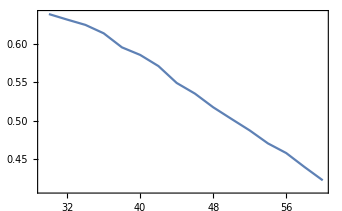

```mathematica
ListLinePlot[strengthlistDR1loop]
```

## The 2-loop perturbation theory in 3d

```mathematica
Veff3d2loop[ϕvalue_,Temp_,g1sq3d_,g2sq3d_,g3sq3d_,μhsq3d_,λh3d_]:=Block[{g1,g2,g3,μ3,μsq,λ,coupling,scale,Veff,μ3US,nF,μsqSU3,msqSU3},
nF=3;
(*couplings and 3d RG scale.*)
coupling={g1->√g1sq3d,g2->√g2sq3d,g3->√g3sq3d,μsq->μhsq3d,λ->λh3d};
msqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.coupling);
scale={μ3->g3sq3d,μ3US->√msqSU3};(*Use the Debye mass as the soft scale μ3US*)

Veff=(PrintEffectivePotential["LO"]+PrintEffectivePotential["NLO"]+PrintEffectivePotential["NNLO"])/.{ϕ->ϕvalue}/.coupling/.scale/.{T->Temp};

Return[Veff]
]
```

```mathematica
findThermo2loop[g1sq_,g2sq_,g3sq_,yt_,mh_,λ_,scaleFactor_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=200;
Tmin=30;
Tloopmax=10;
v1Limit=10;
μhsq=mh^2/2;
{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}={g1sq,g2sq,g3sq,yt,μhsq,λ};
{g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue}=solveBetas[{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}];

Tupper=Catch[Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

```mathematica
TclistDR2loop={};
strengthlistDR2loop={};
Block[{scaleFactor,mhpole,Tc,ϕc,ϕcTc,λrun,mhrun,ytrun,g1run,g2run},
Do[
mhpole=mh;
Print["Higgs mass: ",mhpole," GeV."];
scaleFactor=1.0;
{λrun,mhrun,ytrun,g2run,g1run}=MSbar[mhpole];
{Tc,ϕc,ϕcTc}=findThermo2loop[g1run^2,g2run^2,g3mZ^2,ytrun,mhrun,λrun,scaleFactor];
AppendTo[TclistDR2loop,{mhpole,Tc}];
AppendTo[strengthlistDR2loop,{mhpole,ϕcTc}];
,{mh,30,60,2}]]
```

Higgs mass: 30 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 69.4678, field value at vev: 65.4679, transition strength: 0.942421 Veff at ϕc: -181.109

Higgs mass: 32 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 70.874, field value at vev: 66.35, transition strength: 0.936168 Veff at ϕc: -198.338

Higgs mass: 34 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Find critical temperature: 72.3389, field value at vev: 67.1349, transition strength: 0.928061 Veff at ϕc: -214.917

Higgs mass: 36 GeV.

Find critical temperature: 73.8623, field value at vev: 67.6913, transition strength: 0.916453 Veff at ϕc: -225.831

Higgs mass: 38 GeV.

Find critical temperature: 75.4297, field value at vev: 68.1994, transition strength: 0.904146 Veff at ϕc: -237.544

Higgs mass: 40 GeV.

Find critical temperature: 77.0508, field value at vev: 68.543, transition strength: 0.889583 Veff at ϕc: -245.471

Higgs mass: 42 GeV.

Find critical temperature: 78.7109, field value at vev: 68.9078, transition strength: 0.875454 Veff at ϕc: -256.859

Higgs mass: 44 GeV.

Find critical temperature: 80.4102, field value at vev: 69.1916, transition strength: 0.860484 Veff at ϕc: -267.581

Higgs mass: 46 GeV.

Find critical temperature: 82.1484, field value at vev: 69.3061, transition strength: 0.843669 Veff at ϕc: -273.587

Higgs mass: 48 GeV.

Find critical temperature: 83.9258, field value at vev: 69.1741, transition strength: 0.824229 Veff at ϕc: -271.063

Higgs mass: 50 GeV.

Find critical temperature: 85.7373, field value at vev: 68.9986, transition strength: 0.804767 Veff at ϕc: -268.434

Higgs mass: 52 GeV.

Find critical temperature: 87.5732, field value at vev: 68.71, transition strength: 0.784601 Veff at ϕc: -262.433

Higgs mass: 54 GeV.

Find critical temperature: 89.4287, field value at vev: 68.5128, transition strength: 0.766117 Veff at ϕc: -261.732

Higgs mass: 56 GeV.

Find critical temperature: 91.3086, field value at vev: 68.0801, transition strength: 0.745605 Veff at ϕc: -251.797

Higgs mass: 58 GeV.

Find critical temperature: 93.2178, field value at vev: 67.6235, transition strength: 0.725436 Veff at ϕc: -241.685

Higgs mass: 60 GeV.

Find critical temperature: 95.1514, field value at vev: 66.8299, transition strength: 0.702353 Veff at ϕc: -217.814

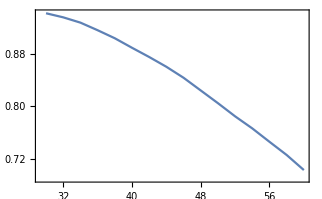

```mathematica
ListLinePlot[strengthlistDR2loop]
```

## The 1-loop perturbation theory in 4d

```mathematica
{λtest,mhtest,yttest,g2test,g1test}=MSbar[30.0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

{0.0300521,54.7754,0.981571,0.651531,0.357987}

### 1-loop full form with resummation

```mathematica
Jbdata=Import[NotebookDirectory[]<>"finiteT_b.dat.txt","Table"];
Jfdata=Import[NotebookDirectory[]<>"finiteT_f.dat.txt","Table"];
JBfit[x_]=Interpolation[Jbdata][x];
JFfit[x_]=Interpolation[Jfdata][x];
```

```mathematica
findThermo1loop[mh_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=200;
Tmin=30;
Tloopmax=10;
v1Limit=20;
acc=10;
ϕ0=10^-5;
{λtest,mhtest,yttest,g2test,g1test}=MSbar[30.0];
V0pre[ϕ_]:=-1/2 μ^2 ϕ^2+1/4 λ ϕ^4;
mWsq[ϕ_]:=1/4 g2test^2 ϕ^2;
mZsq[ϕ_]:=1/4(g2test^2+g1test^2)ϕ^2;
mtsq[ϕ_]:=1/2 yttest^2 ϕ^2;
mgauge=({{g2test^2 x1^2/4+11/6 g2test^2 x2^2, -g2test g1test x1^2/4}, {-g2test g1test x1^2/4, g1test^2 x1^2/4+11/6 g1test^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};
mWL[ϕ_,T_]:=1/4 g2test^2 ϕ^2+11/6 g2test^2 T^2;
VCW‵pre[ϕ_]:=1/(64 π^2)(6 mWsq[ϕ]^2(Log[mWsq[ϕ]/mZ^2]-5/6)+3 mZsq[ϕ]^2(Log[mZsq[ϕ]/mZ^2]-5/6)-12 mtsq[ϕ]^2(Log[mtsq[ϕ]/mZ^2]-3/2));
param=NSolve[{((D[V0pre[ϕ]+VCW‵pre[ϕ],{ϕ,2}]//Simplify)/.{ϕ->v})==mh^2,((D[V0pre[ϕ]+VCW‵pre[ϕ],{ϕ}]//Simplify)/.{ϕ->v})==0},{λ,μ}][[1]];
VCWParwani[ϕ_,T_]:=1/(64 π^2)(4 mWsq[ϕ]^2(Log[mWsq[ϕ]/mZ^2]-1/2)+2 mWL[ϕ,T]^2(Log[mWL[ϕ,T]/mZ^2]-3/2)+2 mZsq[ϕ]^2(Log[mZsq[ϕ]/mZ^2]-1/2)+mZL[ϕ,T]^2(Log[mZL[ϕ,T]/mZ^2]-3/2)+mBL[ϕ,T]^2(Log[mBL[ϕ,T]/mZ^2]-3/2)-12 mtsq[ϕ]^2(Log[mtsq[ϕ]/mZ^2]-3/2));
VFTParwani[ϕ_,T_]:=T^4/(2 π^2)(4JBfit[mWsq[ϕ]/T^2]+2JBfit[mWL[ϕ,T]/T^2]+2JBfit[mZsq[ϕ]/T^2]+JBfit[mZL[ϕ,T]/T^2]+JBfit[mBL[ϕ,T]/T^2]+12JFfit[mtsq[ϕ]/T^2]);
Vtotfull[ϕ_,T_]:=((V0pre[ϕ]+VCWParwani[ϕ,T])/.param)+VFTParwani[ϕ,T];
Tupper=Catch[Do[
Veff0=Vtotfull[ϕ0,TT];
minSol=NMinimize[{Vtotfull[ϕ,TT],ϕ>v1Limit},{ϕ,1,100}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>Veff0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
Veff0=Vtotfull[ϕ0,TT];
minSol=NMinimize[{Vtotfull[ϕ,TT],ϕ>v1Limit},{ϕ,1,100}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>Veff0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<Veff0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
Veff0=Vtotfull[ϕ0,TT];
minSol=NMinimize[{Vtotfull[ϕ,TT],ϕ>v1Limit},{ϕ,1,100}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

```mathematica
findThermo1loop[30]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 69.3115, field value at vev: 46.2392, transition strength: 0.667121 Veff at ϕc: -5.04994×10^7

{69.3115,46.2392,0.667121}

```mathematica
strength1looplist={};
Tc1looplist={};
Block[{mhrun,Tc,ϕc,ϕcTc},
Do[
mhrun=mh;
Print["Higgs mass: ",mhrun," GeV."];
{Tc,ϕc,ϕcTc}=findThermo1loop[mh];
AppendTo[Tc1looplist,{mhrun,Tc}];
AppendTo[strength1looplist,{mhrun,ϕcTc}];
,{mh,30,60,2}]]
```

Higgs mass: 30 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 69.3115, field value at vev: 46.2392, transition strength: 0.667121 Veff at ϕc: -5.04994×10^7

Higgs mass: 32 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

Find critical temperature: 70.7471, field value at vev: 44.8495, transition strength: 0.633942 Veff at ϕc: -5.48416×10^7

Higgs mass: 34 GeV.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24557+2.46064 ⅈ and 0.000246122 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Find critical temperature: 72.2314, field value at vev: 45.3981, transition strength: 0.628509 Veff at ϕc: -5.95877×10^7

Higgs mass: 36 GeV.

Find critical temperature: 73.7842, field value at vev: 45.5839, transition strength: 0.6178 Veff at ϕc: -6.48407×10^7

Higgs mass: 38 GeV.

Find critical temperature: 75.376, field value at vev: 45.0718, transition strength: 0.59796 Veff at ϕc: -7.06525×10^7

Higgs mass: 40 GeV.

Find critical temperature: 77.0264, field value at vev: 45.4388, transition strength: 0.589912 Veff at ϕc: -7.7003×10^7

Higgs mass: 42 GeV.

Find critical temperature: 78.7158, field value at vev: 44.4849, transition strength: 0.565133 Veff at ϕc: -8.40211×10^7

Higgs mass: 44 GeV.

Find critical temperature: 80.4541, field value at vev: 43.8129, transition strength: 0.54457 Veff at ϕc: -9.16863×10^7

Higgs mass: 46 GeV.

Find critical temperature: 82.2314, field value at vev: 43.1692, transition strength: 0.524973 Veff at ϕc: -1.00054×10^8

Higgs mass: 48 GeV.

Find critical temperature: 84.0381, field value at vev: 44.2038, transition strength: 0.525997 Veff at ϕc: -1.09084×10^8

Higgs mass: 50 GeV.

Find critical temperature: 85.8936, field value at vev: 42.9477, transition strength: 0.500011 Veff at ϕc: -1.19035×10^8

Higgs mass: 52 GeV.

Find critical temperature: 87.7686, field value at vev: 42.8824, transition strength: 0.488585 Veff at ϕc: -1.29767×10^8

Higgs mass: 54 GeV.

Find critical temperature: 89.6826, field value at vev: 42.016, transition strength: 0.468496 Veff at ϕc: -1.41455×10^8

Higgs mass: 56 GeV.

Find critical temperature: 91.626, field value at vev: 40.1235, transition strength: 0.437905 Veff at ϕc: -1.54177×10^8

Higgs mass: 58 GeV.

Find critical temperature: 93.5889, field value at vev: 40.7988, transition strength: 0.435937 Veff at ϕc: -1.6774×10^8

Higgs mass: 60 GeV.

Find critical temperature: 95.5908, field value at vev: 38.2798, transition strength: 0.400455 Veff at ϕc: -1.82624×10^8

### High-T form without log term, resummation performed by 2E/3

```mathematica
μ[mh_]:=mh/(√2);
λ[mh_]:=μ[mh]^2/v^2;
DD=1/(8 v^2)(2 mW^2+mZ^2+2 mt^2);
EE=2/3 1/(4π v^3)(2 mW^3+mZ^3);
T0sq[mh_]:=1/(2DD)(μ[mh]^2);
VhighT[ϕ_,mh_,T_]:=DD(T^2-T0sq[mh])ϕ^2-EE T ϕ^3+λ[mh]/4 ϕ^4;
strengthhighT[mh_]:=2 EE/λ[mh];
```

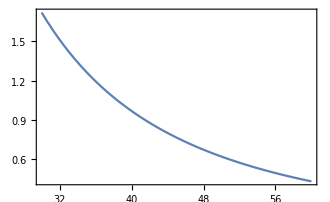

```mathematica
Plot[strengthhighT[mh],{mh,30,60}]
```

## Summary plot

```mathematica
strengthDR1loopfunc[mh_]=Interpolation[strengthlistDR1loop][mh];
strengthDR2loopfunc[mh_]=Interpolation[strengthlistDR2loop][mh];
strength4d1loopfunc[mh_]=Interpolation[strength1looplist][mh];
```

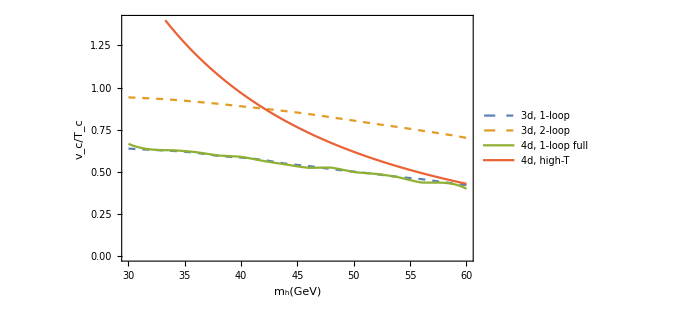

```mathematica
Plot[{strengthDR1loopfunc[mh],strengthDR2loopfunc[mh],strength4d1loopfunc[mh],strengthhighT[mh]},{mh,30,60},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,PlotRange->{{30,60},{0,1.4}},FrameLabel->{Style["m_h(GeV)",FontFamily->"Times",FontSize->22],Style["v_c/T_c",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,PlotStyle->{Directive[Dashed,ColorData[97,1]],Directive[Dashed,ColorData[97,2]],ColorData[97,3],ColorData[97,4]},PlotLegends->{Style["3d, 1-loop",FontFamily->"Times",FontSize->20],Style["3d, 2-loop",FontFamily->"Times",FontSize->20],Style["4d, 1-loop full",FontFamily->"Times",FontSize->20],Style["4d, high-T",FontFamily->"Times",FontSize->20]}]
```